```mathematica
Needs["dsvsolve`"];
```

## Input ATTENZIONE: DSV SOLVE ADOPERA UN SISTEMA DI RIFERIMENTO NEL QUALE L’ASSE X E` ENTRANTE NEL PIANO. QUINDI v(z) e` lo spostamento verso l’alto e Q(z) che rappresenta il taglio, ha la covenzione opposta rispetto a quella del libro

Edit or simply evaluate the following cell to see the input

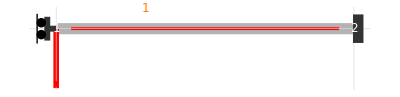

```mathematica
example={$$nodes->{{0, 0}, {L, 0}},
$$edges->{{1, 2}},$$absname->s,
$$constraints->{{{"slidv", 1}}, {{"clamp", 1}}},
$$bodyloads->{{1, {0, 0, 0}}},
$$nodalloads->{{1, {0, -F, 0}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}}};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Risposte

```mathematica
Risultati generali
```

generali Risultati

```mathematica
v[z_]=(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->z/L//Expand
MM[z_]=-EI*v''[z]//Expand
T[z_]=-F
```

(F L^3)/(12 EI)-(F L z^2)/(4 EI)+(F z^3)/(6 EI)

(F L)/2-F z

-F

```mathematica
Versione 1
```

Versione

```mathematica
{v[L/3],NumberForm[v[L/3]//N,3]}
{T[L/3],NumberForm[T[L/3]//N,3]}
{MM[L/3],NumberForm[MM[L/3]//N,3]}
```

{(5 F L^3)/(81 EI),(0.0617 F L^3)/EI}

{-F,-1. F}

{(F L)/6,0.167 F L}

```mathematica
Versione 2
```

2 Versione

```mathematica
{v[L/5],NumberForm[v[L/5]//N,3]}
{T[L/5],NumberForm[T[L/5]//N,3]}
{MM[L/5],NumberForm[MM[L/5]//N,3]}
```

{(28 F L^3)/(375 EI),(0.0747 F L^3)/EI}

{-F,-1. F}

{(3 F L)/10,0.3 F L}

```mathematica
Versione 3
```

3 Versione

```mathematica
{v[2/3L],NumberForm[v[2/3L]//N,3]}
{T[2/3L],NumberForm[T[2/3L]//N,3]}
{MM[2/3L],NumberForm[MM[2/3 L]//N,3]}
```

{(7 F L^3)/(324 EI),(0.0216 F L^3)/EI}

{-F,-1. F}

{-(F L)/6,-0.167 F L}

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
(*BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];*)
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
BFEquations[example,"Nodal"];sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];
gsol=BFShowOutput[example, sol]
```

Natural constraints in node 1: -F+Q_1[0]==0

Natural constraints in node 2: {}

Kinematical constraints in node 1: u_1[0]==0
v_1'[0]==0

Kinematical constraints in node 2: u_1[1]==0
v_1[1]==0
v_1'[1]==0

1234

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Ascissa adimensionale

s

Vincoli statici nei nodi

{{-F+("Q")_("1")[0]==0},{}}

Vincoli cinematici nei nodi

{{("u")_("1")[0]==0,("v")_("1")'[0]==0},{("u")_("1")[1]==0,("v")_("1")[1]==0,("v")_("1")'[1]==0}}

Lista rigidezze flessionali

{EI}

Lista rigidezze assiali

{EA}

Lunghezze delle travi

{L}

Equazioni di campo (o della linea elastica)

{("u")_("1")''[s]==0,(("v")_("1"))^(4)[s]==0}

Condizioni al contorno in spostamenti

{("u")_("1")[0]==0,("v")_("1")'[0]==0,("u")_("1")[1]==0,("v")_("1")[1]==0,("v")_("1")'[1]==0,F L^3+EI (("v")_("1"))^(3)[0]==0}

Soluzione in spostamenti

{{0},{-(F L^3 (1-3 s^2+2 s^3))/(12 EI)}}

Soluzione in sollecitazioni

{{0},{F},{-1/2 F L (-1+2 s)}}

-Graphics-

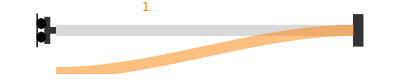

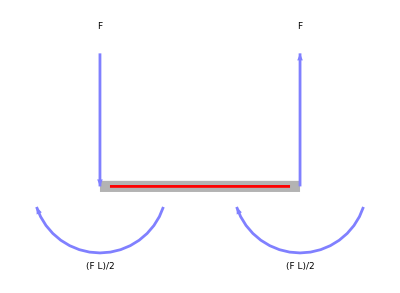

-Graphics-

-Graphics-

-Graphics-

```mathematica
BFConstraintsPalette[BFConstraintTypes]
```

h4tk2_shm37FrontEndObject[LinkObject["h4tk2_shm", 3, 1]]37BF Constraints Palette

```mathematica
-(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->1/3//N
```

-(0.0617284 F L^3)/EI

```mathematica
-(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->1/2//N
```

-(0.0416667 F L^3)/EI

```mathematica
-1/2 F L (-1+2 s)/.s->1/3//N
```

0.166667 F L

```mathematica
-(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->2/3//N
```

-(0.0216049 F L^3)/EI

```mathematica
-(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->1/4//N
```

-(0.0703125 F L^3)/EI

```mathematica
-1/2 F L (-1+2 s)/.s->1/4//N
```

0.25 F L

```mathematica
-(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->1/5//N
```

-(0.0746667 F L^3)/EI

```mathematica
-(F L^3 (1-3 s^2+2 s^3))/(12 EI)/.s->2/5//N
```

-(0.054 F L^3)/EI

```mathematica
-1/2 F L (-1+2 s)/.s->2/5//N
```

0.1 F L